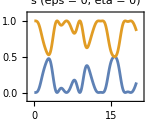

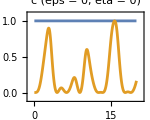

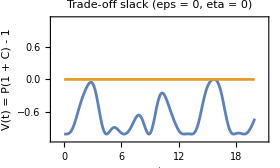

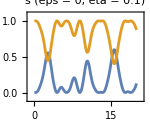

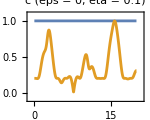

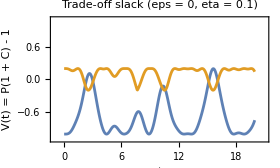

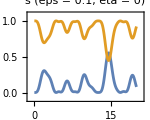

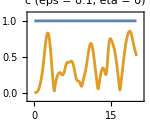

```mathematica
ClearAll["Global`*"];

(*Pauli matrices*)
PauliX=PauliMatrix[1];
PauliY=PauliMatrix[2];
PauliZ=PauliMatrix[3];
Id=IdentityMatrix[2];


concurrence[state_]:=Module[{normState,psiMatrix,sigmaY,psiTilde},normState=Normalize[state];
If[Norm[normState]==0,Return[0]];
psiMatrix=ArrayReshape[normState,{2,2}];
sigmaY=PauliY;
psiTilde=sigmaY.Conjugate[psiMatrix].sigmaY;
Abs[Conjugate[normState].Flatten[psiTilde]]];

(*Build HM,HN from parameter*)
buildHamiltonians[params_Association]:=Module[{Hinternal,Vq1p1,Vq2p1,Vq1p2,Vq2p2,H1,H2},Hinternal=KroneckerProduct[params["omegaA"]*PauliZ,Id]+KroneckerProduct[Id,params["omegaB"]*PauliZ];
Vq1p1=params["c11X"]*PauliX+params["c11Y"]*PauliY+params["c11Z"]*PauliZ;
Vq2p1=params["c21X"]*PauliX+params["c21Y"]*PauliY+params["c21Z"]*PauliZ;
Vq1p2=params["c12X"]*PauliX+params["c12Y"]*PauliY+params["c12Z"]*PauliZ;
Vq2p2=params["c22X"]*PauliX+params["c22Y"]*PauliY+params["c22Z"]*PauliZ;
H1=Hinternal+KroneckerProduct[Vq1p1,Id]+KroneckerProduct[Id,Vq2p1];
H2=Hinternal+KroneckerProduct[Vq1p2,Id]+KroneckerProduct[Id,Vq2p2];
{H1,H2}];

(*Add weak epsilon*Hxx to each process Hamiltonian*)
Hxx=KroneckerProduct[PauliX,PauliX]+1*KroneckerProduct[PauliY,PauliY]+1*KroneckerProduct[PauliZ,PauliZ];
addCrosstalkXX[{HM_,HN_},eps_?NumericQ]:={HM+eps*Hxx,HN+eps*Hxx};

(*Branch minus and plus {P,C} at time t for input psi*)
branchMinus[{HM_,HN_},t_?NumericQ,psi_List]:=Module[{UM,UN,v,P,C},UM=MatrixExp[-I*(t/2)*HM];
UN=MatrixExp[-I*(t/2)*HN];
v=(UM.UN-UN.UM).psi;
P=Norm[v]^2/4.0;
C=If[P>0,concurrence[v],0.0];
{P,C}];

branchPlus[{HM_,HN_},t_?NumericQ,psi_List]:=Module[{UM,UN,v,P,C},UM=MatrixExp[-I*(t/2)*HM];
UN=MatrixExp[-I*(t/2)*HN];
v=(UM.UN+UN.UM).psi;
P=Norm[v]^2/4.0;
C=If[P>0,concurrence[v],0.0];
{P,C}];

(*Violation measure*)
violation[{P_,C_}]:=P*(1+C)-1;

(*Initial states*)
psiSep00={1,0,0,0};
(*weak initial entanglement*)
psiEta[eta_]:=Normalize[{1,0,0,eta}];

(*time grid*)
timeGrid[tmax_,n_Integer]:=Table[i*tmax/(n-1),{i,0.001,n-1}];

(*Build P(t),C(t),V(t) plots*)
makePCVPlots[{HM_,HN_},psi_List,tmax_?NumericQ,n_Integer:600,label_String:""]:=Module[{tList,valsM,valsP,pm,cm,vm,pp,cp,vp,pltP,pltC,pltV},tList=timeGrid[tmax,n];
valsM=Table[branchMinus[{HM,HN},t,psi],{t,tList}];
pm=valsM[[All,1]];
cm=valsM[[All,2]];
vm=violation/@valsM;
valsP=Table[branchPlus[{HM,HN},t,psi],{t,tList}];
pp=valsP[[All,1]];
cp=valsP[[All,2]];
vp=violation/@valsP;
pltP=ListLinePlot[{Transpose[{tList,pm}],Transpose[{tList,pp}]},Frame->True,FrameLabel->{"t","P(t)"},PlotLabel->"s "<>label,PlotRange->{{-1,21.0},{-0.1,1.1}},ImageSize->150,AspectRatio->0.8];
pltC=ListLinePlot[{Transpose[{tList,cm}],Transpose[{tList,cp}]},Frame->True,FrameLabel->{"t","C(t)"},PlotLabel->"c "<>label,PlotRange->{{-1,21.0},{-0.1,1.1}},ImageSize->150,AspectRatio->0.8];
pltV=ListLinePlot[{Transpose[{tList,vm}],Transpose[{tList,vp}]},Frame->True,FrameLabel->{"t","V(t) = P(1 + C) - 1"},PlotLabel->"Trade-off slack "<>label,(*PlotRange->{{-1,21.0},{-1.1,0.3}},ImageSize->280,AspectRatio->0.6];*)
PlotRange->{{-1,21.0},{-1.1,1.1}},ImageSize->280,AspectRatio->0.6];
(*PlotRange->{{-1,21.0},{-1.1,0.45}},ImageSize->280,AspectRatio->0.6];*)
{pltP,pltC,pltV}];


params=<|"omegaA"->1.0,"omegaB"->1.0,"c11X"->1.0,"c11Y"->0.0,"c11Z"->0.0,"c21X"->0.0,"c21Y"->0.0,"c21Z"->0.0,"c12X"->0.0,"c12Y"->0.0,"c12Z"->0.0,"c22X"->1.0,"c22Y"->0.0,"c22Z"->0.0 |>;

{HM0,HN0}=buildHamiltonians[params];


(*A Baseline:non-interacting*)
tmax=20.0;nsamp=600;
psiA=psiSep00;
{pltPA,pltCA,pltVA}=makePCVPlots[{HM0,HN0},psiA,tmax,nsamp,"(eps = 0, eta = 0)"];
Show[pltPA]
Show[pltCA]
Show[pltVA]

(*B Weak initial entanglement*)
etaSmall=10.*10^-2;
psiB=psiEta[etaSmall];
{pltPB,pltCB,pltVB}=makePCVPlots[{HM0,HN0},psiB,tmax,nsamp,"(eps = 0, eta = "<>ToString[etaSmall]<>")"];
Show[pltPB]
Show[pltCB]
Show[pltVB]


(*C Weak epsilon*Hxx,separable input*)
epsSmall=10.*10^-2;
{HMx,HNx}=addCrosstalkXX[{HM0,HN0},epsSmall];
psiC=psiSep00;
{pltPC,pltCC,pltVC}=makePCVPlots[{HMx,HNx},psiC,tmax,nsamp,"(eps = "<>ToString[epsSmall]<>", eta = 0)"];
Show[pltPC]
Show[pltCC]
Show[pltVC]
(*Show[pltPC,ImageSize->{500,250}->"PlotRange"]
Show[pltCC,ImageSize->{500,250}->"PlotRange"]
Show[pltVC,ImageSize->{500,250}->"PlotRange"]*)
```